Based on 1909.08632

```mathematica
σSI[mS_, mx_,gS_]:=1.7 10^-34 gS^2(mS)^-4 mx^2(1+mx/0.938)^-2
```

#### mx=0.1 mS

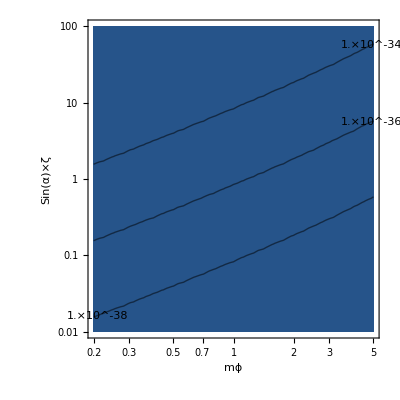

```mathematica
ContourPlot[σSI[mS, 0.1 mS, gS],{mS, 0.2,5},{gS,10^-2,10^2},Contours->{10^-38,10^-36,10^-34}, PlotRange->Full, ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],ScalingFunctions->{"Log","Log"}, FrameLabel->{"mϕ","Sin(α)×ζ"}]
```

#### mS= 1 GeV, mx<ms

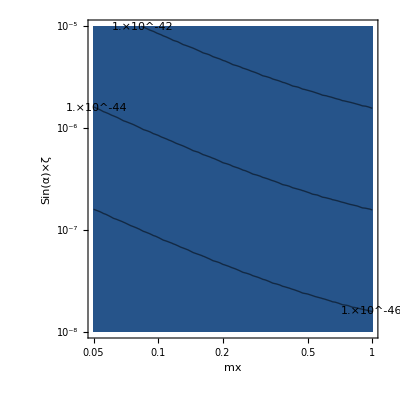

```mathematica
ContourPlot[σSI[0.1,mx, gS],{mx,0.05 ,1},{gS,10^-8,10^-5},Contours->{10^-46,10^-44,10^-42}, PlotRange->Full, ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],ScalingFunctions->{"Log","Log"}, FrameLabel->{"mx","Sin(α)×ζ"}]
```

#### mS= 1 GeV, mx<ms

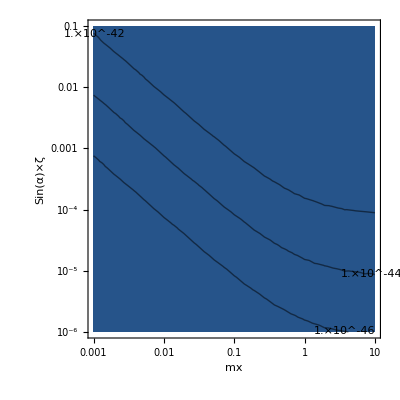

```mathematica
ContourPlot[σSI[1,mx, gS],{mx,0.001 ,10},{gS,10^-6,10^-1},Contours->{10^-46,10^-44,10^-42}, PlotRange->Full, ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],ScalingFunctions->{"Log","Log"}, FrameLabel->{"mx","Sin(α)×ζ"}]
```

#### α=10^-5

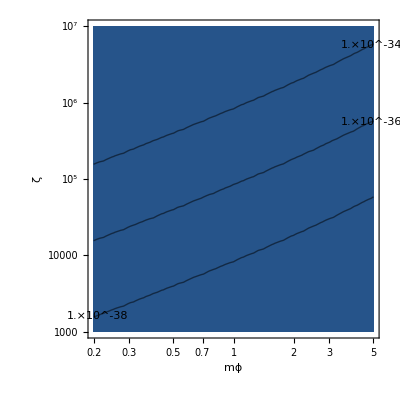

```mathematica
ContourPlot[σSI[mS, 0.1 mS, 10^-5 ζ],{mS, 0.2,5},{ζ,10^3,10^7},Contours->{10^-38,10^-36,10^-34}, PlotRange->Full, ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],ScalingFunctions->{"Log","Log"}, FrameLabel->{"mϕ","ζ"}]
```

#### α=10^-2

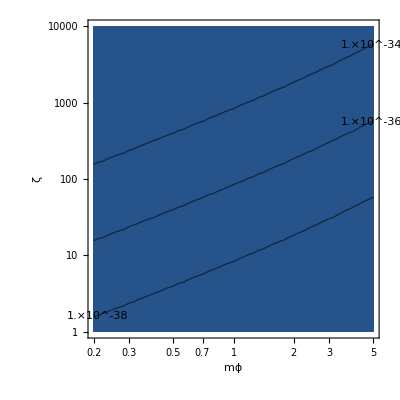

```mathematica
ContourPlot[σSI[mS, 0.1 mS, 10^-2 ζ],{mS, 0.2,5},{ζ,10^0,10^4},Contours->{10^-38,10^-36,10^-34}, PlotRange->Full, ContourLabels->Function[{mϕ,α,z},Text[z//N,{mϕ,α},Background->White]],ScalingFunctions->{"Log","Log"}, FrameLabel->{"mϕ","ζ"}]
```

#### From BBN bounds to σSI

mS=0.2 (above BBN constraints drop), mx=10^2 mS, 10^-5<α<10^-4(at Belle II), from Particle Phys σSI<10^-34(Fig.5)

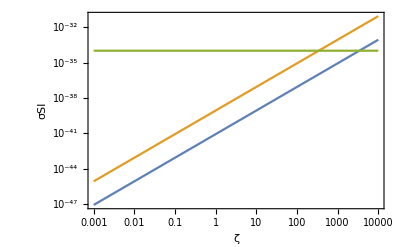

```mathematica
LogLogPlot[{σSI[0.2, 20,ζ 10^-5],σSI[0.2, 20,ζ 10^-4],10^-34},{ζ,10^-3,10^4},Frame->True,FrameLabel->{"ζ","σSI"}]
```